```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[18],Join[Table[{i,i-1},{i,Range[2,18,1]}],Table[{i,i+1},{i,Range[1,18,1]}],Table[{2n-1,18-2n+2},{n,5}],Table[{18-2n+2,2n-1},{n,4}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[18],Table[{2n,18-2n+1},{n,4}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[18],Table[{2n,2n},{n,4}]->t]
```

```mathematica
Clear[LEFT,LEFT1]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.001,1,0]],B:=Inverse[β[ω,0.001,1,0]],T1:=T1[1]},Do[J=Inverse[IdentityMatrix[18]-B.ConjugateTranspose[T1].J.T1].B,3000]; J=J]
```

```mathematica
LEFT1[ω_,δ_,t_,ϵ_]:=LEFT1[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.001,1,0]],B:=Inverse[β[ω,0.001,1,0]],T1:=T1[1]},Do[J=Inverse[IdentityMatrix[18]-B.ConjugateTranspose[T1].J.T1].B,3010]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[18]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[18]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[18]-SL[ω,δ,t,ϵ].T[t].SR[ω,δ,t,ϵ].T[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[18]-SR[ω,δ,t,ϵ].T[t].SL[ω,δ,t,ϵ].T[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].T[t].grr[ω,δ,t,ϵ].T[t]-T[t].GNON[ω,δ,t,ϵ].T[t].GNON[ω,δ,t,ϵ]]
```

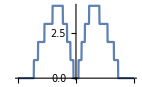

```mathematica
ListLinePlot[Table[{ω,Abs[tr[ω,0.0001,1,0]]},{ω,Range[-4,4,0.01]}]]
```

```mathematica
imp[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{gg=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,18}]},ReplacePart[gg,{{4,4}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
m=RandomInteger[{0,1}];n=RandomInteger[{0,1}];o=RandomInteger[{0,1}];p=RandomInteger[{0,1}];q=RandomInteger[{0,1}];Print[{m+n+o+p+q+4}]
```

{6}

```mathematica
tr1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{gg=g[ω,δ,t,ϵ],T=T1[1],imp=imp[ω,δ,t,ϵ,ϵ1],m=RandomInteger[{0,2}],n=RandomInteger[{0,2}],o=RandomInteger[{0,2}],p=RandomInteger[{0,2}],q=RandomInteger[{0,2}]},(*Print[{m+n+o+p+q+4}];*)sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Inverse[IdentityMatrix[18]-gg.ConjugateTranspose[T].J.T].gg,n]; J=J];sl2=Inverse[IdentityMatrix[18]-imp.ConjugateTranspose[T].sl1.T].imp; sl3=Module[{J=sl2},Do[J=Inverse[IdentityMatrix[18]-gg.ConjugateTranspose[T].J.T].gg,m]; J=J];sl4=Inverse[IdentityMatrix[18]-gg.ConjugateTranspose[T].sl3.T].gg; sl5=Module[{J=sl4},Do[J=Inverse[IdentityMatrix[18]-gg.ConjugateTranspose[T].J.T].gg,o]; J=J];sl6=Inverse[IdentityMatrix[18]-gg.ConjugateTranspose[T].sl5.T].gg; sl7=Module[{J=sl6},Do[J=Inverse[IdentityMatrix[18]-gg.ConjugateTranspose[T].J.T].gg,p]; J=J];sl8=Inverse[IdentityMatrix[18]-imp.ConjugateTranspose[T].sl7.T].imp; sl9=Module[{J=sl8},Do[J=Inverse[IdentityMatrix[18]-gg.ConjugateTranspose[T].J.T].gg,q]; J=J];Il1:=Inverse[IdentityMatrix[18]-sl9.TT[1].SR[ω,0.001,1,0].TT[1]].sl9;
Ir1:=Inverse[IdentityMatrix[18]-SR[ω,δ,1,0].TT[1].sl9.TT[1]].SR[ω,δ,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,1,0].TT[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.TT[1].grr1.TT[1]-TT[1].GNON1.TT[1].GNON1]]]
```

```mathematica
Timing[Mean[Table[tr1[0,0.0001,1,0,1],10]]]
```

{0.024538,2.76793×10^-6}

```mathematica
Table[{N,Mean[Table[tr1[1.0,0.0001,1,0,1],N]]},{N,Range[100,6000,200]}]
```

{{100,2.80715},{300,2.86509},{500,2.85486},{700,2.85561},{900,2.87368},{1100,2.87047},{1300,2.8709},{1500,2.85601},{1700,2.84692},{1900,2.8645},{2100,2.87103},{2300,2.85627},{2500,2.85901},{2700,2.85987},{2900,2.85999},{3100,2.85563},{3300,2.85551},{3500,2.85365},{3700,2.85872},{3900,2.86792},{4100,2.85939},{4300,2.85461},{4500,2.85265},{4700,2.86483},{4900,2.86332},{5100,2.86323},{5300,2.85974},{5500,2.861},{5700,2.85166},{5900,2.8645}}

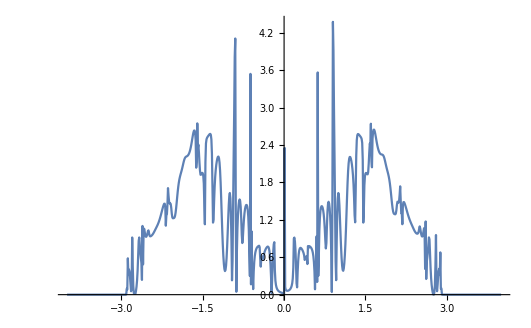

```mathematica
ListLinePlot[Table[{ω,Mean[Table[tr1[ω,0.0001,1,0,-100],10]]},{ω,Range[-4,4,0.01]}]]
```

```mathematica
Export["9agnr4imp1.csv",Table[{ω,Mean[Table[tr1[ω,0.0001,1,0,1000],10]]},{ω,Range[-4,4,0.01]}]]
```

$Aborted

```mathematica
imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{gg=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,9}]},ReplacePart[gg,{{μ1,μ1},{18-μ1+1,19-μ1+1}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
tr2[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{gg=g[ω,δ,t,ϵ],T=T1[1],imp=imp[ω,δ,t,ϵ,ϵ1],m=RandomInteger[{0,2}],n=RandomInteger[{0,2}],o=RandomInteger[{0,2}],p=RandomInteger[{0,2}],q=RandomInteger[{0,2}]},(*Print[{m+n+o+p+q+4}];*)sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Inverse[IdentityMatrix[18]-gg.ConjugateTranspose[T].J.T].gg,n]; J=J];sl2=Inverse[IdentityMatrix[18]-imp.ConjugateTranspose[T].sl1.T].imp; sl3=Module[{J=sl2},Do[J=Inverse[IdentityMatrix[18]-gg.ConjugateTranspose[T].J.T].gg,m]; J=J];sl4=Inverse[IdentityMatrix[18]-imp.ConjugateTranspose[T].sl3.T].imp; sl5=Module[{J=sl4},Do[J=Inverse[IdentityMatrix[18]-gg.ConjugateTranspose[T].J.T].gg,o]; J=J];sl6=Inverse[IdentityMatrix[18]-imp.ConjugateTranspose[T].sl5.T].imp; sl7=Module[{J=sl6},Do[J=Inverse[IdentityMatrix[18]-gg.ConjugateTranspose[T].J.T].gg,p]; J=J];sl8=Inverse[IdentityMatrix[18]-imp.ConjugateTranspose[T].sl7.T].imp; sl9=Module[{J=sl8},Do[J=Inverse[IdentityMatrix[18]-gg.ConjugateTranspose[T].J.T].gg,q]; J=J];Il1:=Inverse[IdentityMatrix[18]-sl9.TT[1].SR[ω,0.001,1,0].TT[1]].sl9;
Ir1:=Inverse[IdentityMatrix[18]-SR[ω,δ,1,0].TT[1].sl9.TT[1]].SR[ω,δ,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,1,0].TT[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.TT[1].grr1.TT[1]-TT[1].GNON1.TT[1].GNON1]]]
```